```mathematica
Id[d_]:=IdentityMatrix[d];γe=1.76086 10^8;

σ={{1/2.({{0, 1}, {1, 0}}),1/2.({{0, -ⅈ}, {ⅈ, 0}}),1/2.({{1, 0}, {0, -1}})},{1/(√2.)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),1/(√2.)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}}),({{1., 0, 0}, {0, 0, 0}, {0, 0, -1.}})}};

M1_⊗M2_:=KroneckerProduct[M1,M2]; M1_⊗M2_⊗M3_:=(M1⊗M2)⊗M3;

HyperfineHamiltonian[n_,spin_,hfc_]:=(
If[n==0,M=1; 
S=Table[σ[[1,p]],{p,3}]; Table[0,{2},{2}],
M=Product[spin[[k]],{k,1,n}]; II=Table[(Id[Product[spin[[k]],{k,1,j-1}]])⊗σ[[spin[[j]]-1,p]]⊗(Id[Product[spin[[k]],{k,j+1,n}]]),{j,n},{p,3}];
S=Table[σ[[1,p]]⊗Id[M],{p,3}];
Sum[hfc[[j,p,q]] σ[[1,p]]⊗II[[j,q]],{j,n},{p,3},{q,3}]  ]
);

ZeemanHamiltonian[ω0_,θ0_,ϕ0_]:=(
ω0(S[[1]] Sin[θ0]Cos[ϕ0]+S[[2]] Sin[θ0]Sin[ϕ0]+S[[3]] Cos[θ0])
);

TY[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(3*M))PT;
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

## Isotropic hyperfine coupling constants (HFCC) data for FADH^.

### Lee at el. (Alternative radical pairs for cryptochrome-based magnetoreception)

Nucleus | HFCC (mT)
H5 | -0.8029
N5 | 0.4313
H8(X3) | 0.2554
N10 | 0.2506
Hβ | 0.1908

## Figure 1d

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PAa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PAb=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PAc=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
Show[PAa,PAb,PAc]
```

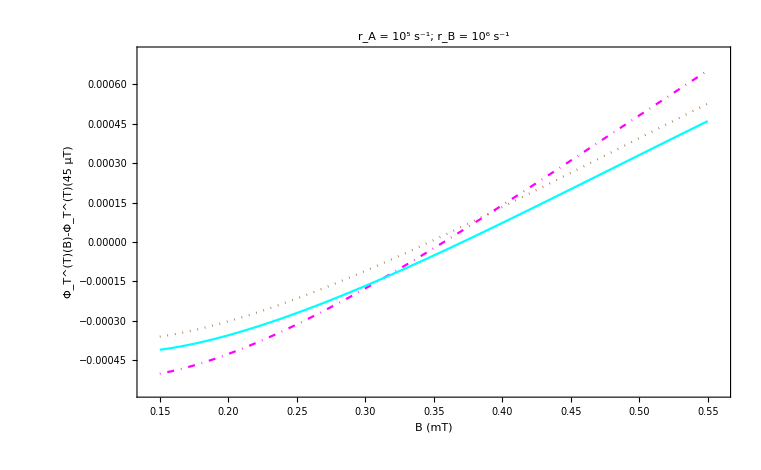

## Figure 2a

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PBa=Plot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB],{B,0.0,1.0},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1",Epilog->{{GrayLevel[0],Thin,Line[{{0.0,0.0},{1.0,0.0}}]}}];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PBb=Plot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB],{B,0.0,1.0},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PBc=Plot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB],{B,0.0,1.0},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)" },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
Show[PBa,PBb,PBc]
```

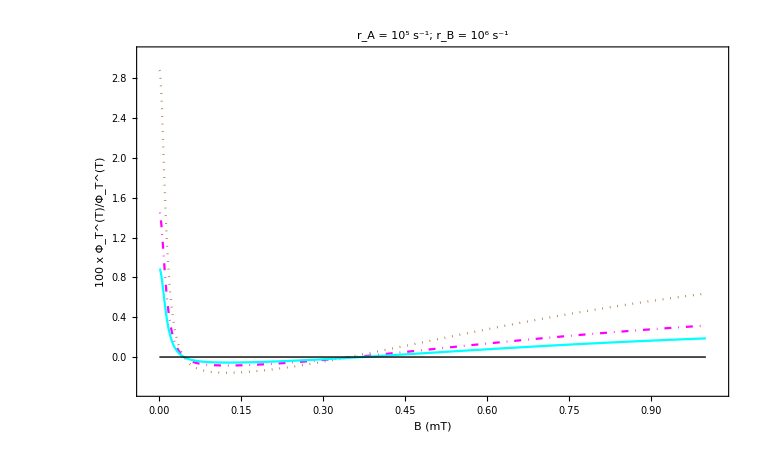

## Figure 3c

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe;
spinB={2};hfcB={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}γe; 
krA=1.0*10^6;krB=1.0*10^6;
ks = 3.94*10^7; kt = 3.94*10^5;
A=10;
PCa=ListPlot[Table[{B,A*100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Orange,Dashed},Joined->False,PlotLegends->{"k_S = 3.94×10^7s^-1; k_T = 3.94×10^5s^-1; A = 10.0; E = 35.75", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); 
b = 1 mT (spin-1/2);
r_A = 10^6 s^-1, r_B = 10^6 s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe;
spinB={2};hfcB={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}γe; 
krA=1.0*10^6;krB=1.0*10^6;
ks = 3.05*10^7; kt = 1.79*10^5;
A=7.17;
PCb=ListPlot[Table[{B,A*100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue,Join},PlotLegends->{"k_S = 3.05×10^7s^-1; k_T = 1.79×10^5s^-1; A = 7.17; E = 31.23", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^6 s^-1; r_B = 10^6 s^-1
a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); b = 1 mT (spin-1/2)"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe;
spinB={2};hfcB={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}γe; 
krA=1.0*10^6;krB=1.0*10^6;
ks = 3.45*10^7; kt = 5.27*10^5;
A=7.93;
PCc=ListPlot[Table[{B,A*100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.06]},PlotStyle->{Red},PlotLegends->{"k_S = 3.45×10^7s^-1; k_T = 5.27×10^5s^-1; A = 7.93, E = 32.66", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^6 s^-1; r_B = 10^6 s^-1
a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); b = 1 mT (spin-1/2)"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe;
spinB={2};hfcB={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}γe; 
krA=1.0*10^6;krB=1.0*10^6;
ks = 2.95*10^7; kt = 3.52*10^5;
A=6.13;
PCd=ListPlot[Table[{B,A*100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"k_S = 2.95×10^7s^-1; k_T = 3.52×10^5s^-1; A = 6.13, E = 34.01", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^6 s^-1; r_B = 10^6 s^-1
a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); b = 1 mT (spin-1/2)"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe;
spinB={2};hfcB={({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}γe; 
krA=1.0*10^6;krB=1.0*10^6;
ks = 2.19*10^7; kt = 2.44*10^5;
A=5.87;
PCe=ListPlot[Table[{B,A*100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"k_S = 2.19×10^7s^-1; k_T = 2.44×10^5s^-1; A = 5.87, E = 35.72", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"r_A = 10^6 s^-1; r_B = 10^6 s^-1
a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); b = 1 mT (spin-1/2)"];
```

```mathematica
PCf= ListPlot[{{0.0,Around[68,11]},{0.2,Around[-34,4]},{0.5,Around[52,11]},{0.7,Around[71,9]},{0.9,Around[130,19]}},PlotMarkers-> {"★",PointSize[0.06]},PlotStyle->{Black,Thick},PlotRange->All,IntervalMarkersStyle->{Black,Thick},PlotLegends->{"Experiment"},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,16],PlotLabel->"a1 = 1 mT (spin-1/2), a2 = 0.1 mT (spin-1); 
b = 1 mT (spin-1/2);
r_A = 10^6 s^-1, r_B = 10^6 s^-1"];
```

```mathematica
Show[PCf,PCa,PCb,PCc,PCd,PCd,PCe]
```

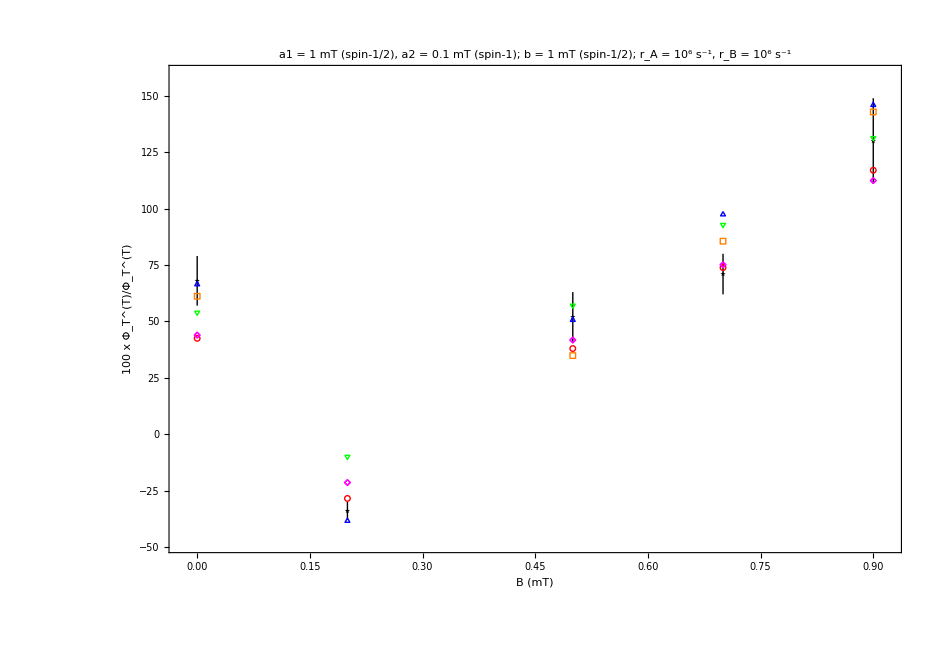

# Supporting Information

## Figure S1

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PDa=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^5 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourLines->False,ContourShading->{ColorData["Legacy"]["Violet"],ColorData["Legacy"]["Steelblue"],ColorData["Legacy"]["CadetBlue"],ColorData["Legacy"]["Olive"],ColorData["Legacy"]["DarkKhaki"],ColorData["Legacy"]["Goldenrod"],ColorData["Legacy"]["YellowOchre"]},Contours->{-3,-6,-9,-12,-15,-18}];
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PDb=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^6 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourShading->None,ContourStyle->Directive[Thick,White,Dashed],Contours->{0.5,0,-2,-5,-15},Epilog->{Text[Framed[ToString[-15],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[7*10^6],Log[1*10^5]}],Text[Framed[ToString[-5],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[4.5*10^6],Log[3*10^6]}],Text[Framed[ToString[-2],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.3*10^6],Log[4*10^6]}],Text[Framed[ToString[0],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.0*10^5],Log[5*10^5]}],Text[Framed[ToString[0.5],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[9*10^5],Log[1.0*10^5]}]}];
```

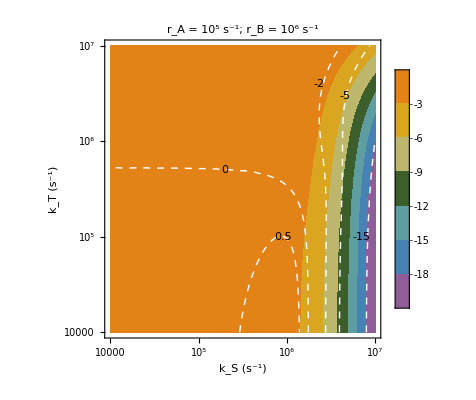

```mathematica
Show[PDb,PDa,PDb]
```

## Figure S2

```mathematica
TYFP[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(4*M))Id[4M];
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PEa=ContourPlot[100*(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.2*γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^5 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourLines->False,ContourShading->{ColorData["Legacy"]["Violet"],ColorData["Legacy"]["Steelblue"],ColorData["Legacy"]["CadetBlue"],ColorData["Legacy"]["Olive"],ColorData["Legacy"]["DarkKhaki"],ColorData["Legacy"]["Goldenrod"],ColorData["Legacy"]["YellowOchre"]},Contours->{0,-3,-6,-9,-12,-15}];
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PEb=ContourPlot[100*(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.5*γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^6 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourShading->None,ContourStyle->Directive[Thick,White,Dashed],Contours->{-15,-5,-0.01,0,0.1,2},Epilog->{Text[Framed[ToString[-8],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[8*10^6],Log[5*10^4]}],Text[Framed[ToString[-4],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[6*10^6],Log[5*10^5]}],Text[Framed[ToString[-0.01],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[5.1*10^4],Log[3*10^5]}],Text[Framed[ToString[-0.01],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[1.3*10^6],Log[5*10^5]}],Text[Framed[ToString[0],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[4.3*10^5],Log[4.5*10^5]}],Text[Framed[ToString[0.1],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[1*10^5],Log[2*10^6]}],Text[Framed[ToString[0.1],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[5*10^5],Log[2*10^5]}],Text[Framed[ToString[2],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.4*10^6],Log[6.2*10^6]}]}];
```

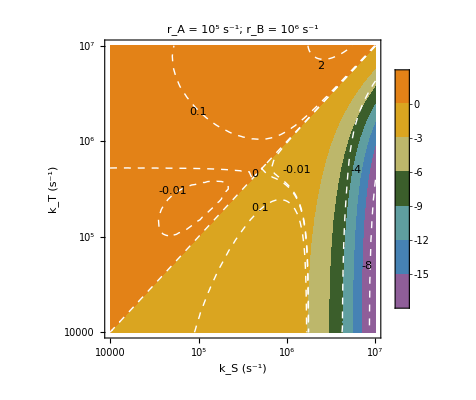

```mathematica
Show[PEb,PEa,PEb]
```

## Figure S3

```mathematica
nA=1;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PFa=Plot[(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Brown,Dotted}, PlotLegends ->{"k_T = 1.0×10^4s^-1",Line},FrameLabel ->{"B (mT)","Φ_T(B)- Φ_T(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^5 s^-1"];
```

```mathematica
nA=1;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PFb=Plot[(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Magenta,DotDashed}, PlotLegends ->{"k_T = 5.0×10^4s^-1",Line},FrameLabel ->{"B (mT)","% change in Φ_T^(T)(relative to 45μT)" },Frame->True,LabelStyle -> Directive[ Bold]];
```

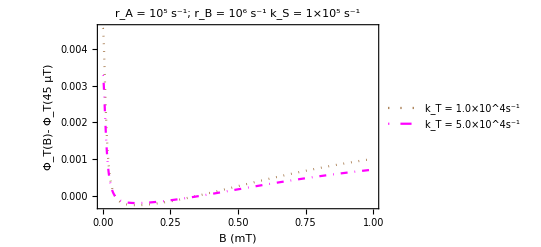

```mathematica
Show[PFa,PFb]
```

## Figure S4

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
PGa=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^3,1.0* 10^9},{kt,1.0* 10^3,1.0* 10^9},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^6 s^-1; r_B = 2x10^7 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourLines->False,ContourShading->{ColorData["Legacy"]["Violet"],ColorData["Legacy"]["Steelblue"],ColorData["Legacy"]["CadetBlue"],ColorData["Legacy"]["Olive"],ColorData["Legacy"]["DarkKhaki"],ColorData["Legacy"]["Goldenrod"],ColorData["Legacy"]["YellowOchre"]},Contours->{0,-1}];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
PGb=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^3,1.0* 10^9},{kt,1.0* 10^3,1.0* 10^9},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^6 s^-1; r_B = 2x10^7 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourShading->None,ContourStyle->Directive[Thick,White,Dashed],Contours->{0,-1},Epilog->{Text[Framed[ToString[0],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[5*10^4],Log[8*10^7]}],Text[Framed[ToString[-1],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2*10^6],Log[2*10^5]}]}];
```

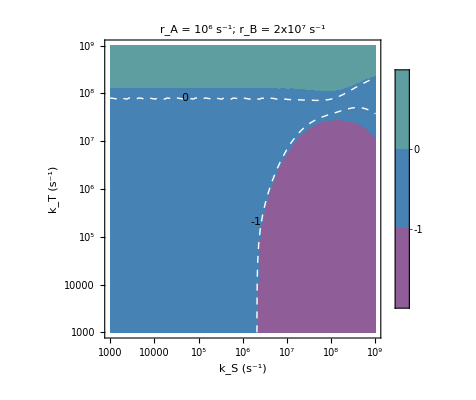

```mathematica
Show[PGb,PGa,PGb]
```

## Figure S5

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^3; kt = 1*10^8;
PHa=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Orange,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^3s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 2x10^7 s^-1;
k_T = 1×10^8s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^4; kt = 1*10^8;
PHb=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^4s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 10^7 s^-1;
k_T = 1×10^8s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^5; kt = 1*10^8;
PHc=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.06]},PlotStyle->{Red,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^5s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 10^7 s^-1;
k_T = 1×10^8s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^6; kt = 1*10^8;
PHd=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^6s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 10^7 s^-1;
k_T = 1×10^8s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^7; kt = 1*10^8;
PHe=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Green,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^7s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 10^7 s^-1;
k_T = 1×10^8s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.0, 0, 0}, {0, 0.0, 0}, {0, 0, 0.0}})}γe; 
krA=1.0*10^6;krB=2.0*10^7;
ks = 1*10^8; kt = 1*10^8;
PHf=ListPlot[Table[{B,100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"×",PointSize[0.06]},PlotStyle->{Black,Dashed},Joined->False,PlotLegends->{"k_S = 1×10^8s^-1", Line},FrameLabel ->{"B (mT)","100 x Φ_T^(T)/Φ_T^(T)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^6 s^-1, r_B = 10^7 s^-1;
k_T = 1×10^8s^-1"];
```

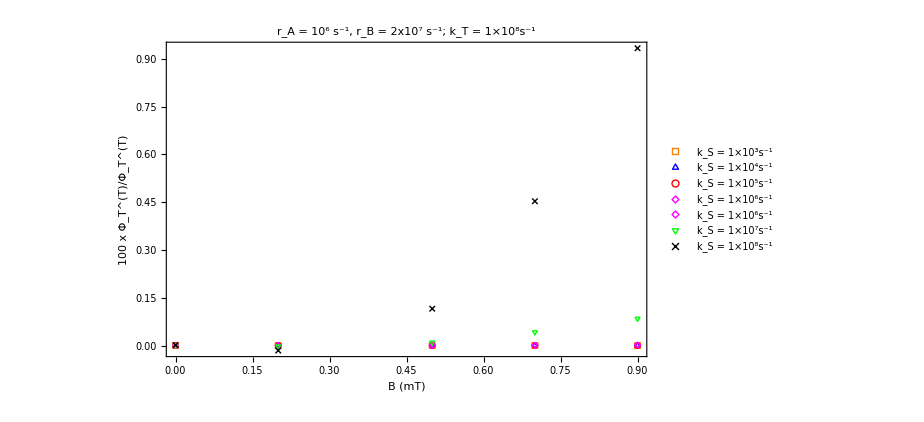

```mathematica
Show[PHa,PHb,PHc,PHd,PHd,PHe,PHf,PlotRange->All]
```